```mathematica
(*Build the Bell operator*)
id = IdentityMatrix[2];
A0 = {{1,0},{0,-1}};
B0 = {{1,0},{0,-1}};
A1 ={{Subscript[c, A],Subscript[s, A]},{Subscript[s, A],-Subscript[c, A]}};
B1 ={{Subscript[c, B],Subscript[s, B]},{Subscript[s, B],-Subscript[c, B]}};
Subscript[C, α,α]  = KroneckerProduct[A0,B0+B1]+KroneckerProduct[A1,B0-B1] + α (KroneckerProduct[id,B0]+KroneckerProduct[A0,id]);
Subscript[C, α,α] =FullSimplify[Subscript[C, α,α] ];
```

```mathematica
Subscript[C, α,α] //MatrixForm
```

(1+2 α-c_A (-1+c_B)+c_B | -((-1+c_A) s_B) | -((-1+c_B) s_A) | -s_A s_B
-((-1+c_A) s_B) | -1+c_A (-1+c_B)-c_B | -s_A s_B | (-1+c_B) s_A
-((-1+c_B) s_A) | -s_A s_B | -1+c_A (-1+c_B)-c_B | (-1+c_A) s_B
-s_A s_B | (-1+c_B) s_A | (-1+c_A) s_B | 1-2 α-c_A (-1+c_B)+c_B)

```mathematica
(*Retrieve and simplify the characteristic polynomial*)
```

```mathematica
q =Collect[ CharacteristicPolynomial[Subscript[C, α,α] ,λ],{Subscript[s, A],Subscript[s, B]}];
q=q/.{Subscript[s, A]^2->1-Subscript[c, A]^2,Subscript[s, A]^4->(1-Subscript[c, A]^2)^2 ,Subscript[s, B]^2->1-Subscript[c, B]^2,Subscript[s, B]^4->(1-Subscript[c, B]^2)^2 };
q = Collect[FullSimplify[q],λ,Simplify]
```

-4 (2+α^2) λ^2+λ^4+8 α^2 λ (-1+c_A (-1+c_B)-c_B)+8 (c_A^2 (-2+α^2-2 c_B) (-1+c_B)-c_B (α^2+(-2+α^2) c_B)+α^2 c_A (-1+c_B^2))

```mathematica
(*Write the system of polynomial equation associated to the lagrnagian problem*)
p0=D[λ+s q,λ];
p1=D[λ+s q,Subscript[c, A]]/s;
p2=D[λ+s q,Subscript[c, B]]/s;
p3=D[λ+s q,s];
```

```mathematica
(*Use a Gröbner basis to eliminate Subscript[c, A], Subscript[c, B] and the lagrange multiplier s*)
```

```mathematica
f0=FullSimplify[GroebnerBasis[{p0,p1,p2,p3},{s,λ,Subscript[c, A],Subscript[c, B]},{s,Subscript[c, A],Subscript[c, B]}][[1]]]
```

-((2+2 α-λ) (-2+2 α+λ) (4 α^6 (5+2 λ)+4 (2+λ)^2 (-8+λ^2)-4 α^2 (-16+λ (2+λ) (10+λ))+α^4 (-84+λ (-4+11 λ))))

```mathematica
(*Eliminate two trivial roots that are easily seen to be suboptimal*)
```

```mathematica
f=Expand[PolynomialQuotientRemainder[f0,(2+2 α-λ) (-2+2 α+λ),λ][[1]]]
```

128-64 α^2+84 α^4-20 α^6+128 λ+80 α^2 λ+4 α^4 λ-8 α^6 λ+16 λ^2+48 α^2 λ^2-11 α^4 λ^2-16 λ^3+4 α^2 λ^3-4 λ^4

```mathematica
(*Since f is a degree 4 polynomial, we can analytically find it roots*)
```

```mathematica
Λ = λ/.Solve[f==0,λ];
(*We plot the roots to that only the maximum root violates the classical bound*)
```

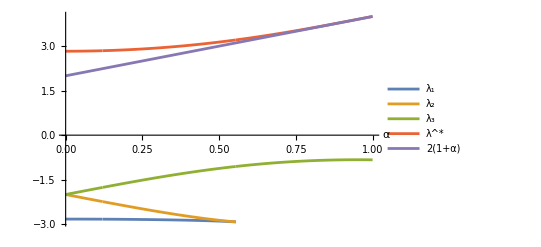

```mathematica
Plot[{Λ[[1]],Λ[[2]],Λ[[3]],Λ[[4]],2(1+α)},{α,0,1},PlotLegends->{"λ_1","λ_2","λ_3","λ^*","2(1+α)"},AxesLabel->Automatic]
```

```mathematica
(*The maximal quantum value of the symmetrically tilted CHSH inequality*)
```

```mathematica
SuperStar[λ]=Re[Λ [[4]]]
```

Re[1/4 (-4+α^2)+1/2 √(1/4 (4-α^2)^2+1/4 (16+48 α^2-11 α^4)+1/12 (-16-48 α^2+11 α^4)+(256+6912 α^2-2848 α^4-528 α^6+217 α^8)/(6 2^(2/3) (-8192+552960 α^2+551424 α^4-880128 α^6+473376 α^8-124560 α^10+12742 α^12-√(-14495514624 α^2+152202903552 α^4-575290736640 α^6+953080086528 α^8-833605337088 α^10+880206151680 α^12-825048170496 α^14+464663347200 α^16-151505068032 α^18+28462067712 α^20-2875931136 α^22+121485312 α^24))^(1/3))+1/(12 2^(1/3))(-8192+552960 α^2+551424 α^4-880128 α^6+473376 α^8-124560 α^10+12742 α^12-√(-14495514624 α^2+152202903552 α^4-575290736640 α^6+953080086528 α^8-833605337088 α^10+880206151680 α^12-825048170496 α^14+464663347200 α^16-151505068032 α^18+28462067712 α^20-2875931136 α^22+121485312 α^24))^(1/3))+1/2 √(1/2 (4-α^2)^2+1/3 (16+48 α^2-11 α^4)-(256+6912 α^2-2848 α^4-528 α^6+217 α^8)/(6 2^(2/3) (-8192+552960 α^2+551424 α^4-880128 α^6+473376 α^8-124560 α^10+12742 α^12-√(-14495514624 α^2+152202903552 α^4-575290736640 α^6+953080086528 α^8-833605337088 α^10+880206151680 α^12-825048170496 α^14+464663347200 α^16-151505068032 α^18+28462067712 α^20-2875931136 α^22+121485312 α^24))^(1/3))-1/(12 2^(1/3))(-8192+552960 α^2+551424 α^4-880128 α^6+473376 α^8-124560 α^10+12742 α^12-√(-14495514624 α^2+152202903552 α^4-575290736640 α^6+953080086528 α^8-833605337088 α^10+880206151680 α^12-825048170496 α^14+464663347200 α^16-151505068032 α^18+28462067712 α^20-2875931136 α^22+121485312 α^24))^(1/3)+(-(4-α^2)^3+(4-α^2) (-16-48 α^2+11 α^4)-8 (-32-20 α^2-α^4+2 α^6))/(4 √(1/4 (4-α^2)^2+1/4 (16+48 α^2-11 α^4)+1/12 (-16-48 α^2+11 α^4)+(256+6912 α^2-2848 α^4-528 α^6+217 α^8)/(6 2^(2/3) (-8192+552960 α^2+551424 α^4-880128 α^6+473376 α^8-124560 α^10+12742 α^12-√(-14495514624 α^2+152202903552 α^4-575290736640 α^6+953080086528 α^8-833605337088 α^10+880206151680 α^12-825048170496 α^14+464663347200 α^16-151505068032 α^18+28462067712 α^20-2875931136 α^22+121485312 α^24))^(1/3))+1/(12 2^(1/3))(-8192+552960 α^2+551424 α^4-880128 α^6+473376 α^8-124560 α^10+12742 α^12-√(-14495514624 α^2+152202903552 α^4-575290736640 α^6+953080086528 α^8-833605337088 α^10+880206151680 α^12-825048170496 α^14+464663347200 α^16-151505068032 α^18+28462067712 α^20-2875931136 α^22+121485312 α^24))^(1/3))))]

```mathematica
(*To find the optimal cosines we consider polynomials p1 and p2 above and simplify them*)
```

```mathematica
p1=Simplify[p1]
```

8 (-1+c_B) (2 c_A (-2+α^2-2 c_B)+α^2 (1+λ+c_B))

```mathematica
p2=Simplify[p2]
```

8 (-1+c_A) (α^2 (1+λ)+c_A (α^2-4 c_B)+2 (-2+α^2) c_B)

```mathematica
(*Since cA=1 and cB=1 correspond to compatible measurements, we are interested in the second factor on each of these expressions.*)
```

```mathematica
p1=Collect[(2 Subscript[c, A] (-2+α^2-2 Subscript[c, B])+α^2 (1+λ+Subscript[c, B])),λ]
```

α^2+α^2 λ+2 c_A (-2+α^2-2 c_B)+α^2 c_B

```mathematica
p2=Collect[(α^2 (1+λ)+Subscript[c, A] (α^2-4 Subscript[c, B])+2 (-2+α^2) Subscript[c, B]),λ]
```

α^2+α^2 λ+c_A (α^2-4 c_B)+2 (-2+α^2) c_B

```mathematica
(*Since optimal cosines are roots of p1 and p2, we take their difference to eliminate λ, to retrieve the following condition.*)
```

```mathematica
Factor[p1-p2]
```

(-2+α) (2+α) (c_A-c_B)

```mathematica
(*Since α∈[0,1), we conclude that the optimal cosines must be equal, Subscript[c, A]=Subscript[c, B]. We now plug in this simplification into p1, and retrieve a quadratic polynomial in Subscript[c, A]*)
```

```mathematica
p1=Simplify[p1/.{Subscript[c, B]->Subscript[c, A]}]
```

α^2 (1+λ)+(-4+3 α^2) c_A-4 c_A^2

```mathematica
(*We solve the quadratic equation p=0 for Subscript[c, B] to retrieve the expressions of its two roots*)
```

```mathematica
CA=Subscript[c, A]/.Solve[p1==0,Subscript[c, A]]
```

{1/8 (-4+3 α^2-√(16-8 α^2+9 α^4+16 α^2 λ)),1/8 (-4+3 α^2+√(16-8 α^2+9 α^4+16 α^2 λ))}

```mathematica
(*Taking λ=λ^*, we plot these two roots against α and find that only the largest root yeilds valid cosines*)
```

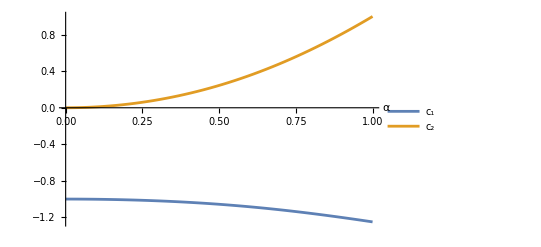

```mathematica
Plot[{CA[[1]]/.{λ->SuperStar[λ]},CA[[2]]/.{λ->SuperStar[λ]}},{α,0,1},PlotLegends->{"c_1","c_2"},AxesLabel->Automatic]
```

```mathematica
(*The explicit expression of the optimal settings for maximal quantum value of symmetrically tilted CHSH inequality in terms of α*)
SuperStar[c]=CA[[2]]/.{λ->SuperStar[λ]}
```

1/8 (-4+3 α^2+√(16-8 α^2+9 α^4+16 α^2 Re[1/4 (-4+α^2)+1/2 √(1/4 (4-α^2)^2+1/4 (16+48 α^2-11 α^4)+1/12 (-16-48 α^2+11 α^4)+(256+6912 α^2-2848 α^4-528 α^6+217 α^8)/(6 2^(2/3) (-8192+552960 α^2+551424 α^4-880128 α^6+473376 α^8-124560 α^10+12742 α^12-√(-14495514624 α^2+152202903552 α^4-575290736640 α^6+953080086528 α^8-833605337088 α^10+880206151680 α^12-825048170496 α^14+464663347200 α^16-151505068032 α^18+28462067712 α^20-2875931136 α^22+121485312 α^24))^(1/3))+1/(12 2^(1/3))(-8192+552960 α^2+551424 α^4-880128 α^6+473376 α^8-124560 α^10+12742 α^12-√(-14495514624 α^2+152202903552 α^4-575290736640 α^6+953080086528 α^8-833605337088 α^10+880206151680 α^12-825048170496 α^14+464663347200 α^16-151505068032 α^18+28462067712 α^20-2875931136 α^22+121485312 α^24))^(1/3))+1/2 √(1/2 (4-α^2)^2+1/3 (16+48 α^2-11 α^4)-(256+6912 α^2-2848 α^4-528 α^6+217 α^8)/(6 2^(2/3) (-8192+552960 α^2+551424 α^4-880128 α^6+473376 α^8-124560 α^10+12742 α^12-√(-14495514624 α^2+152202903552 α^4-575290736640 α^6+953080086528 α^8-833605337088 α^10+880206151680 α^12-825048170496 α^14+464663347200 α^16-151505068032 α^18+28462067712 α^20-2875931136 α^22+121485312 α^24))^(1/3))-1/(12 2^(1/3))(-8192+552960 α^2+551424 α^4-880128 α^6+473376 α^8-124560 α^10+12742 α^12-√(-14495514624 α^2+152202903552 α^4-575290736640 α^6+953080086528 α^8-833605337088 α^10+880206151680 α^12-825048170496 α^14+464663347200 α^16-151505068032 α^18+28462067712 α^20-2875931136 α^22+121485312 α^24))^(1/3)+(-(4-α^2)^3+(4-α^2) (-16-48 α^2+11 α^4)-8 (-32-20 α^2-α^4+2 α^6))/(4 √(1/4 (4-α^2)^2+1/4 (16+48 α^2-11 α^4)+1/12 (-16-48 α^2+11 α^4)+(256+6912 α^2-2848 α^4-528 α^6+217 α^8)/(6 2^(2/3) (-8192+552960 α^2+551424 α^4-880128 α^6+473376 α^8-124560 α^10+12742 α^12-√(-14495514624 α^2+152202903552 α^4-575290736640 α^6+953080086528 α^8-833605337088 α^10+880206151680 α^12-825048170496 α^14+464663347200 α^16-151505068032 α^18+28462067712 α^20-2875931136 α^22+121485312 α^24))^(1/3))+1/(12 2^(1/3))(-8192+552960 α^2+551424 α^4-880128 α^6+473376 α^8-124560 α^10+12742 α^12-√(-14495514624 α^2+152202903552 α^4-575290736640 α^6+953080086528 α^8-833605337088 α^10+880206151680 α^12-825048170496 α^14+464663347200 α^16-151505068032 α^18+28462067712 α^20-2875931136 α^22+121485312 α^24))^(1/3))))]))

```mathematica
(*Since the maximal quantum value of of symmetrically tilted CHSH inequality uniquely determines the optimal measurements, we conclude that the maximal quantum value self-tests the optimal measurements. To demonstrate self-testing of the state we plug the optimal consine back into the characterstic polynomial and plot its roots.*)
```

```mathematica
(*Let us first simplify the characterstic polynomial with the fact Subscript[c, A]=Subscript[c, B]=c *)
```

```mathematica
Subscript[q, 0]=FullSimplify[q/.{Subscript[c, A]->c,Subscript[c, B]->c}]
```

-((2 c+λ) (8 c^3+8 λ-λ^3+4 α^2 (2+λ)-4 c^2 (2 α^2+λ)+2 c (-8+4 α^2+λ^2)))

```mathematica
(*We now find the roots of Subscript[q, 0] analytically in terms of c,α*)
```

```mathematica
Eig=Re[FullSimplify[λ/.{Solve[Subscript[q, 0]==0,λ]}]][[1]]
```

{-2 Re[c],1/6 Re[4 c+(4 2^(1/3) (2 c^2-3 (2+α^2)))/((-20 c^3-27 α^2+27 c^2 α^2-36 c (-1+α^2)+√((4 c (-9+5 c^2)+9 (3+(4-3 c) c) α^2)^2+4 (2 c^2-3 (2+α^2))^3))^(1/3))-2 2^(2/3) (-20 c^3-27 α^2+27 c^2 α^2-36 c (-1+α^2)+√((4 c (-9+5 c^2)+9 (3+(4-3 c) c) α^2)^2+4 (2 c^2-3 (2+α^2))^3))^(1/3)],1/12 Re[8 c+(8 (-2)^(1/3) (6-2 c^2+3 α^2))/((-20 c^3-27 α^2+27 c^2 α^2-36 c (-1+α^2)+√((4 c (-9+5 c^2)+9 (3+(4-3 c) c) α^2)^2+4 (2 c^2-3 (2+α^2))^3))^(1/3))+2 2^(2/3) (1-ⅈ √3) (-20 c^3-27 α^2+27 c^2 α^2-36 c (-1+α^2)+√((4 c (-9+5 c^2)+9 (3+(4-3 c) c) α^2)^2+4 (2 c^2-3 (2+α^2))^3))^(1/3)],1/12 Re[8 c+(8 (-1)^(2/3) 2^(1/3) (2 c^2-3 (2+α^2)))/((-20 c^3-27 α^2+27 c^2 α^2-36 c (-1+α^2)+√((4 c (-9+5 c^2)+9 (3+(4-3 c) c) α^2)^2+4 (2 c^2-3 (2+α^2))^3))^(1/3))+2 2^(2/3) (1+ⅈ √3) (-20 c^3-27 α^2+27 c^2 α^2-36 c (-1+α^2)+√((4 c (-9+5 c^2)+9 (3+(4-3 c) c) α^2)^2+4 (2 c^2-3 (2+α^2))^3))^(1/3)]}

```mathematica
(*With optimal settings c=c^*, we plot the eigenvalues of the Bell operator, and find that the largest eigenvalue coincides with λ^* and is nondegenerate, demonstrating that the maximal quantum value self-tests the shared entangled state*)
```

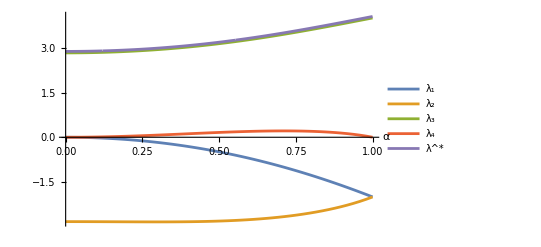

```mathematica
Plot[{Eig[[1]]/.{c->SuperStar[c]},Eig[[2]]/.{c->SuperStar[c]},Eig[[3]]/.{c->SuperStar[c]},Eig[[4]]/.{c->SuperStar[c]},SuperStar[λ]+0.05},{α,0,1},PlotLegends->{"λ_1","λ_2","λ_3","λ_4","λ^*"},AxesLabel->Automatic]
```